```mathematica
a0=-7.803*10^-1
a1=1
a2=-2.886*10^-1
a4=8.130*10^-3
a6=-2.004*10^-4
a8=3.625*10^-6
a10=-4.969*10^-8
a12=5.339*10^-10
a14=-4.655*10^-12
```

-0.7803

1

-0.2886

0.00813

-0.0002004

3.625×10^-6

-4.969×10^-8

5.339×10^-10

-4.655×10^-12

```mathematica
z1=a0+a1*Abs[x]+a2*Abs[x]^2+a4*Abs[x]^4+a6*Abs[x]^6+a8*Abs[x]^8+a10*Abs[x]^10+a12*Abs[x]^12+a14*Abs[x]^14
t=1.2
z2=(a0+a1*Abs[x/t]+a2*Abs[x/t]^2+a4*Abs[x/t]^4+a6*Abs[x/t]^6+a8*Abs[x/t]^8+a10*Abs[x/t]^10+a12*Abs[x/t]^12+a14*Abs[x/t]^14)*t-0.3*t
t2=1.5
z3=(a0+a1*Abs[x/t2]+a2*Abs[x/t2]^2+a4*Abs[x/t2]^4+a6*Abs[x/t2]^6+a8*Abs[x/t2]^8+a10*Abs[x/t2]^10+a12*Abs[x/t2]^12+a14*Abs[x/t2]^14)*t2-0.5*t2
```

-0.7803+Abs[x]-0.2886 Abs[x]^2+0.00813 Abs[x]^4-0.0002004 Abs[x]^6+3.625×10^-6 Abs[x]^8-4.969×10^-8 Abs[x]^10+5.339×10^-10 Abs[x]^12-4.655×10^-12 Abs[x]^14

1.2

-0.36+1.2 (-0.7803+0.833333 Abs[x]-0.200417 Abs[x]^2+0.00392072 Abs[x]^4-0.0000671136 Abs[x]^6+8.43059×10^-7 Abs[x]^8-8.02521×10^-9 Abs[x]^10+5.98804×10^-11 Abs[x]^12-3.62562×10^-13 Abs[x]^14)

1.5

-0.75+1.5 (-0.7803+0.666667 Abs[x]-0.128267 Abs[x]^2+0.00160593 Abs[x]^4-0.0000175934 Abs[x]^6+1.41442×10^-7 Abs[x]^8-8.61701×10^-10 Abs[x]^10+4.11495×10^-12 Abs[x]^12-1.59456×10^-14 Abs[x]^14)

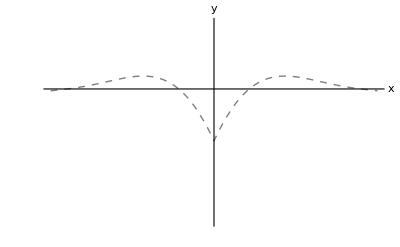

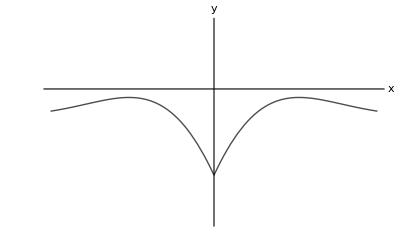

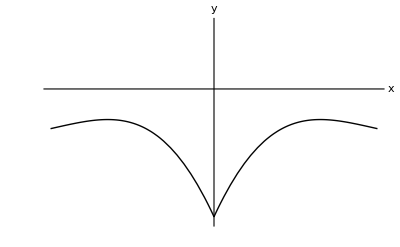

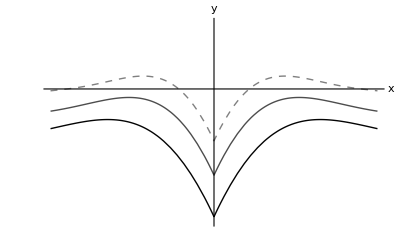

```mathematica
g1=Plot[z1,{x,-5.3,5.3},Frame->False,AxesLabel->{x,y},PlotRange->{-2,1},PlotStyle->{GrayLevel[.5],Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
g2=Plot[z2,{x,-5.3,5.3},Frame->False,AxesLabel->{x,y},PlotRange->{-2,1},PlotStyle->{GrayLevel[.3],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
g3=Plot[z3,{x,-5.3,5.3},Frame->False,AxesLabel->{x,y},PlotRange->{-2,1},PlotStyle->{GrayLevel[.01],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
Show[g1,g2,g3]
```

```mathematica
Plot3D[z1,{x,-5.3,5.3},{y,-10,10},Mesh->None,Boxed->False,Axes->False,Filling->Bottom,FillingStyle->Directive[Cyan,Specularity[White,40],Opacity[1.7]],PlotStyle->Directive[LightCyan,Specularity[White,40]]]
```

-Graphics3D-

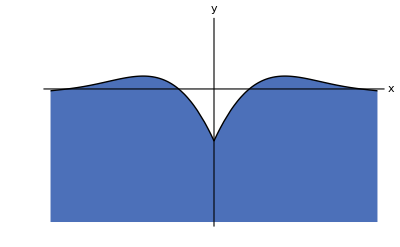

```mathematica
Plot[z1,{x,-5.3,5.3},Frame->False,Filling->Bottom,FillingStyle->Directive[RGBColor[0,0.2,0.61],Opacity[0.7]],AxesLabel->{x,y},PlotRange->{-2,1},PlotStyle->{Black,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
```